Initialisation Cells

```mathematica
SetDirectory["~/Code/multimode-mls"];
t1=Import["output.h5",{"Datasets","/1/t"}];
x1=Import["output.h5",{"Datasets","/1/x"}];
y1=Import["output.h5",{"Datasets","/1/y"}];
reatom1=Import["output.h5",{"Datasets","/1/reatom"}];
imatom1=Import["output.h5",{"Datasets","/1/imatom"}];
modatom1=Import["output.h5",{"Datasets","/1/modatom"}];
relight1=Import["output.h5",{"Datasets","/1/relight"}];
imlight1=Import["output.h5",{"Datasets","/1/imlight"}];
ResetDirectory[];

declaredVariables={"t1","x1","y1","reatom1","imatom1","modatom1","relight1","imlight1"};
```

```mathematica
tmax=Length[t1];
ymax=Length[y1];
xmax=Length[x1];
First[x1];
Last[x1];
```

```mathematica
Kern1D[x_,xp_,ξ_]=Sqrt[ⅈ/(Pi*Sin[ξ])]*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ]-(2*xp*x)/Sin[ξ])];
Kern[x_,xp_,y_,yp_,ξ_]=ⅈ/(Pi*Sin[ξ])*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ]-(2*xp*x)/Sin[ξ]+(yp^2+y^2)/Tan[ξ]-(2*y*yp)/Sin[ξ])];
```

## Atomic field (manipulate, interpolation)

```mathematica
Manipulate[{modpsisq=Interpolation[Flatten[Table[{{x1[[i]],y1[[j]]},modatom1[[ttemp,i,j]]},{i,1,xmax},{j,1,ymax}],1],InterpolationOrder->4];
Show[DensityPlot[modpsisq[x,y],{x,First[x1],-First[x1]},{y,First[y1],-First[y1]},ImageSize->500,PlotLegends->True,PlotPoints->20,MaxRecursion->4,PlotRange->{Automatic,Automatic,Full}],Graphics[{Line[{{0,20},{0,-20}}],Line[{{20,0},{-20,0}}]}]]},{ttemp,1,tmax,1}]
```

Table::iterb: Iterator {i,1,xmax} does not have appropriate bounds.

Interpolation::innd: First argument in Table[{{x1⟦i⟧,y1⟦j⟧},modatom1⟦FE`ttemp$$15,i,j⟧},{i,1,xmax},{j,1,ymax}] does not contain a list of data and coordinates.

Table::iterb: Iterator {i,1,xmax} does not have appropriate bounds.

Interpolation::innd: First argument in Table[{{x1⟦i⟧,y1⟦j⟧},modatom1⟦FE`ttemp$$15,i,j⟧},{i,1,xmax},{j,1,ymax}] does not contain a list of data and coordinates.

First::normal: Nonatomic expression expected at position 1 in First[x1].

DensityPlot::plln: Limiting value First[x1] in {x,First[x1],-First[x1]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[DensityPlot[modpsisq[x,y],{x,First[x1],-First[x1]},{y,First[y1],-First[y1]},ImageSize→500,PlotLegends→True,PlotPoints→20,MaxRecursion→4,PlotRange→{Automatic,Automatic,Full}],].

DensityPlot::plln: Limiting value First[x1] in {x,First[x1],-First[x1]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[DensityPlot[modpsisq[x,y],{x,First[x1],-First[x1]},{y,First[y1],-First[y1]},ImageSize→500,PlotLegends→True,PlotPoints→20,MaxRecursion→4,PlotRange→{Automatic,Automatic,Full}],].

```mathematica
Manipulate[Show[DensityPlot[modpsisq[x,y,t],{x,First[x1],-First[x1]},{y,First[y1],-First[y1]},ImageSize->500,PlotLegends->True,PlotPoints->20,MaxRecursion->4,PlotRange->{Automatic,Automatic,Full}],Graphics[{Line[{{0,20},{0,-20}}],Line[{{20,0},{-20,0}}]}]],{t,1,tmax,1}]
```

Interpolation::indat: Data point {{{-12.,-12.},3.07247×10^-27},{{-12.,-12.},1.21049×10^-27},{{-12.,-12.},9.43525×10^-24},{{-12.,-12.},3.40958×10^-19},{{-12.,-12.},2.02197×10^-17},{{-12.,-12.},1.46673×10^-16},{{-12.,-12.},4.18318×10^-16},{{-12.,-12.},7.70429×10^-16},{«1»},{{-12.,-12.},1.42397×10^-15},{{-12.,-12.},1.25298×10^-15},{{-12.,-12.},7.16331×10^-16},{{-12.,-12.},9.90986×10^-16},{{-12.,-12.},1.8752×10^-15},{{-12.,-12.},2.71695×10^-15},{{-12.,-12.},1.74498×10^-15}} contains abscissa {{-12.,-12.},3.07247×10^-27}, which is not a real number.

First::normal: Nonatomic expression expected at position 1 in First[x1].

DensityPlot::plln: Limiting value First[x1] in {x,First[x1],-First[x1]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[DensityPlot[modpsisq[x,y,FE`t$$17],{x,First[x1],-First[x1]},{y,First[y1],-First[y1]},ImageSize→500,PlotLegends→True,PlotPoints→20,MaxRecursion→4,PlotRange→{Automatic,Automatic,Full}],].

## Light field (single x,y,t)

```mathematica
xtemp=16;
ytemp=16;
ttemp=200;
alphap=Integrate[Integrate[(relightplus1[[ttemp,xtemp,ytemp]]+ⅈ*imlightplus1[[ttemp,xtemp,ytemp]])*Kern[x1[[xtemp]],xp,y1[[ytemp]],yp,-Pi/4],{xp,-2000,2000}],{yp,-2000,2000}];
alpham=Integrate[Integrate[(relightminus1[[ttemp,xtemp,ytemp]]+ⅈ*imlightminus1[[ttemp,xtemp,ytemp]])*Kern[x1[[xtemp]],xp,y1[[ytemp]],yp,Pi/4],{xp,-2000,2000}],{yp,-2000,2000}];
Abs[alphap]^2
Abs[alpham]^2
```

0.0111228

0.00318756

```mathematica
ttemp=200;
xr=28;
yr=28;
alphap=Sum[(relightplus1[[ttemp,xtemp,ytemp]]+ⅈ*imlightplus1[[ttemp,xtemp,ytemp]])*Kern[x1[[xtemp]],xr,y1[[ytemp]],yr,-Pi/4],{ytemp,1,ymax},{xtemp,1,xmax}]
alpham=Sum[(relightminus1[[ttemp,xtemp,ytemp]]+ⅈ*imlightminus1[[ttemp,xtemp,ytemp]])*Kern[x1[[xtemp]],xr,y1[[ytemp]],yr,Pi/4],{ytemp,1,ymax},{xtemp,1,xmax}]
Abs[alpham]^2
Abs[alphap]^2
```

5.07022+2.96267 ⅈ

-2.25081+4.02603 ⅈ

21.2751

34.4845

## Light field (at a single t, ListDensityPlot)

```mathematica
ttemp=2000;
alphapl=Flatten[Table[{x1[[xstep]],y1[[ystep]],Abs[Integrate[Integrate[(relightplus1[[ttemp,xstep,ystep]]+ⅈ*imlightplus1[[ttemp,xstep,ystep]])*Kern[x1[[xstep]],xp,y1[[ystep]],yp,-Pi/4],{xp,-200,200}],{yp,-200,200}]]^2},{xstep,1,xmax},{ystep,1,ymax}],1];
alphamin=Flatten[Table[{x1[[xstep]],y1[[ystep]],Abs[Integrate[Integrate[(relightminus1[[ttemp,xstep,ystep]]+ⅈ*imlightminus1[[ttemp,xstep,ystep]])*Kern[x1[[xstep]],xp,y1[[ystep]],yp,Pi/4],{xp,-200,200}],{yp,-200,200}]]^2},{xstep,1,xmax},{ystep,1,ymax}],1];
```

$Aborted

$Aborted

```mathematica
ttemp=tmax;
aplus=Flatten[Table[{x1[[xstep]],y1[[ystep]],Abs[relightplus1[[ttemp,xstep,ystep]]+ⅈ*imlightplus1[[ttemp,xstep,ystep]]]^2},{xstep,1,xmax},{ystep,1,ymax}],1];
aminus=Flatten[Table[{x1[[xstep]],y1[[ystep]],Abs[relightminus1[[ttemp,xstep,ystep]]+ⅈ*imlightminus1[[ttemp,xstep,ystep]]]^2},{xstep,1,xmax},{ystep,1,ymax}],1];
```

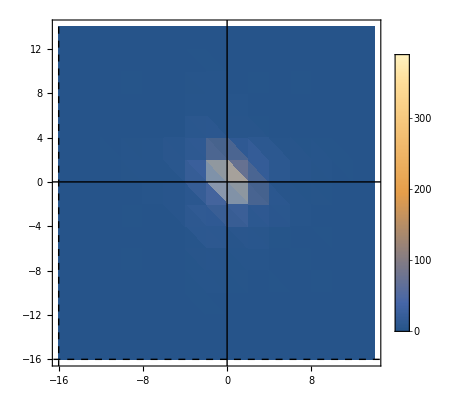

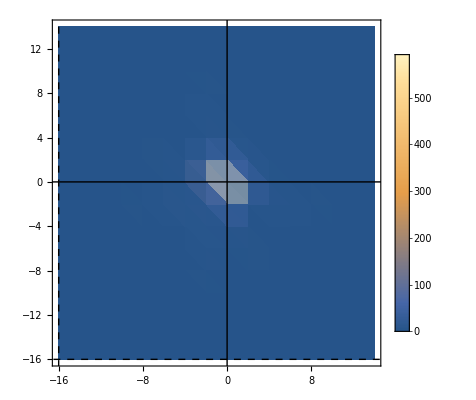

```mathematica
Show[ListDensityPlot[aplus,PlotLegends->True,PlotRange->{Automatic,Automatic,All}],Graphics[{Line[{{28,0},{-32,0}}],Line[{{0,28},{0,-32}}],{Dashed,Line[{{-16,28},{-16,-32}}]},{Dashed,Line[{{16,28},{16,-32}}]},{Dashed,Line[{{28,16},{-32,16}}]},{Dashed,Line[{{28,-16},{-32,-16}}]}}]]
Show[ListDensityPlot[aminus,PlotLegends->True,PlotRange->{Automatic,Automatic,All}],Graphics[{Line[{{28,0},{-32,0}}],Line[{{0,28},{0,-32}}],{Dashed,Line[{{-16,28},{-16,-32}}]},{Dashed,Line[{{16,28},{16,-32}}]},{Dashed,Line[{{28,16},{-32,16}}]},{Dashed,Line[{{28,-16},{-32,-16}}]}}]]
```

```mathematica
ttemp=tmax;
alphapl=Table[{xr,yr,Abs[Sum[(relightplus1[[ttemp,xtemp,ytemp]]+ⅈ*imlightplus1[[ttemp,xtemp,ytemp]])*Kern[x1[[xtemp]],xr,y1[[ytemp]],yr,-Pi/4],{ytemp,1,ymax},{xtemp,1,xmax}]]^2},{xr,-32,28,4},{yr,-32,28,4}];
alphamin=Table[{xr,yr,Abs[Sum[(relightminus1[[ttemp,xtemp,ytemp]]+ⅈ*imlightminus1[[ttemp,xtemp,ytemp]])*Kern[x1[[xtemp]],xr,y1[[ytemp]],yr,Pi/4],{ytemp,1,ymax},{xtemp,1,xmax}]]^2},{xr,-32,28,4},{yr,-32,28,4}];
```

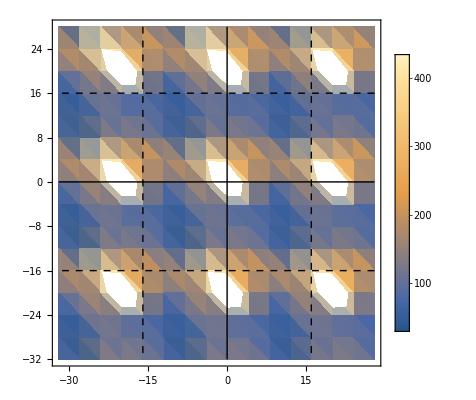

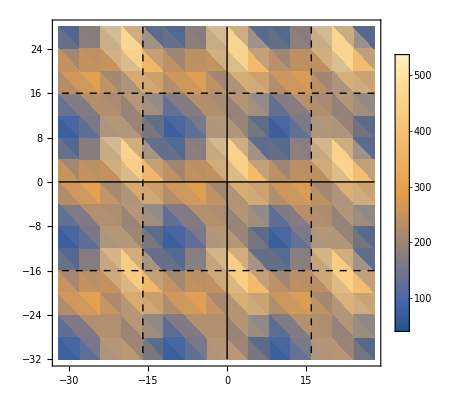

```mathematica
Show[ListDensityPlot[Flatten[alphapl,1],PlotLegends->True],Graphics[{Line[{{28,0},{-32,0}}],Line[{{0,28},{0,-32}}],{Dashed,Line[{{-16,28},{-16,-32}}]},{Dashed,Line[{{16,28},{16,-32}}]},{Dashed,Line[{{28,16},{-32,16}}]},{Dashed,Line[{{28,-16},{-32,-16}}]}}]]
Show[ListDensityPlot[Flatten[alphamin,1],PlotLegends->True],Graphics[{Line[{{28,0},{-32,0}}],Line[{{0,28},{0,-32}}],{Dashed,Line[{{-16,28},{-16,-32}}]},{Dashed,Line[{{16,28},{16,-32}}]},{Dashed,Line[{{28,16},{-32,16}}]},{Dashed,Line[{{28,-16},{-32,-16}}]}}]]
```

```mathematica
N[2 Pi/4]
```

1.5708

## Light field (at a single t, interpolation)

```mathematica
ttemp=2000;
alphapl=Flatten[Table[{{x1[[xstep]],y1[[ystep]]},Abs[Integrate[Integrate[(relightplus1[[ttemp,xstep,ystep]]+ⅈ*imlightplus1[[ttemp,xstep,ystep]])*Kern[x1[[xstep]],xp,y1[[ystep]],yp,-Pi/4],{xp,-200,200}],{yp,-200,200}]]^2},{xstep,1,xmax},{ystep,1,ymax}],1];
alphamin=Flatten[Table[{{x1[[xstep]],y1[[ystep]]},Abs[Integrate[Integrate[(relightminus1[[ttemp,xstep,ystep]]+ⅈ*imlightminus1[[ttemp,xstep,ystep]])*Kern[x1[[xstep]],xp,y1[[ystep]],yp,Pi/4],{xp,-200,200}],{yp,-200,200}]]^2},{xstep,1,xmax},{ystep,1,ymax}],1];
```

```mathematica
interplus=Interpolation[alphapl,InterpolationOrder->2]
interminus=Interpolation[alphamin,InterpolationOrder->2]
```

InterpolatingFunction[{{-32., 28.}, {-32., 28.}}, <>]

InterpolatingFunction[{{-32., 28.}, {-32., 28.}}, <>]

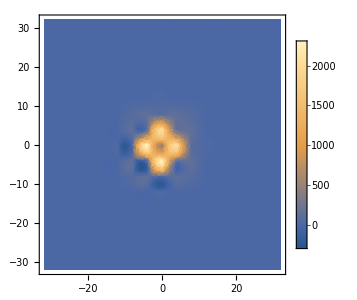

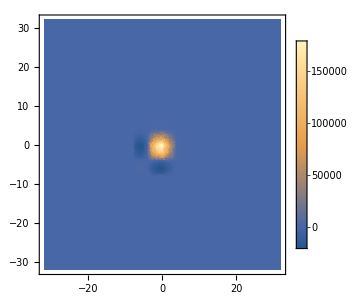

```mathematica
DensityPlot[interminus[x,y],{x,First[x1],-First[x1]},{y,First[y1],-First[y1]},ImageSize->300,PlotLegends->True,PlotPoints->50,MaxRecursion->3,PlotRange->{Automatic,Automatic,Full}]
DensityPlot[interplus[x,y],{x,First[x1],-First[x1]},{y,First[y1],-First[y1]},ImageSize->300,PlotLegends->True,PlotPoints->50,MaxRecursion->3,PlotRange->{Automatic,Automatic,Full}]
```